# Experiments, Data and Models for Nonlinear Electrical Circuits

Allan Struthers and Jason Gregerson

Math Sciences, Michigan Technological University

Over 80% of the student body at MTU has a Science or Engineering major.  Essentially all of those students complete a Linear Algebra and ODE sequence.  The additional requirements for a Math minor fit reasonably well into most technical degrees and many students choose to complete a math minor.   A senior level course “Nonlinear Dynamics and Chaos” is a common elective for such students.  A project is a common component of this course.

## Abstract

We describe a sequence of simple experiments built on breadboard using standard passive (resistors, capacitors, and inductors) circuit components and a commodity analog multiplier chip. Preliminary experiments (simple RC and LRC circuits) give a natural way to extract parameter value using standard signal generator waveforms. Subsequent experiments introduce an analog multiplier chip which gives the scaled product of two input voltages. A final experiment incorporates multiplier chips into LRC based circuits to generate more interesting output.

## Background

Electrical Engineering and Physics majors in Nonlinear Dynamics and Chaos have often chosen to build a various chaotic circuits as a final project.  This is much more challenging for students than they anticipate. They struggle to build functioning circuits and explain the link between the ODE model and the circuit diagram they followed.  Last fall I decided to incorporate a circuits tutorial into this class by getting the students to construct  a circuit modelled by the chaotic Rosseler [1] ODEs
	x' | = | -y-z
y' | = | x+a y
z' | = | b+z(x-c)
The primary source for this was a proposal [2] found by an earlier student group. Students reported previous experience building circuits with soldering irons and claimed to remember circuits from ODEs.

Students struggled more with this material than I thought they would and I started building some tutorial material.

## Circuit Diagram from [2]

This Rossler circuit implementation is simpler than most other chaotic circuits.

-Graphics-

The inexpensive analog multiplier AD633 is the multiplicative term z(x-c) in the 3rd ODE. Fortunately the AD633 data sheet [5] is very clear.

## Analog Multiplier from [2]

The AD633 data sheet [5] is admirably clear.

-Graphics-

## Target

A more convincing accessible introduction to simple circuits starting from clear statements of Kirchoff’s laws and specifications of the standard passive (capacitors, resistors, and inductors) circuit elements with a goal of understanding how to construct and collect data from a circuit modelled by a Rossler system.

## Basics and Kirchoff’s Laws

Kirchoff’s laws apply to the flow of electricity in a network of electrical components.

Electrical components (voltage sources, capacitors, resistors, inductors, etc) are connected by wires which are joined at nodes.

Capacitors store charge. Kirchoff’s laws and component properties give ODEs for the time varying charge q_i(t) stored on each capacitor in a network.

Voltage differences drive changes in the charge stored q_i(t) stored on capacitor i.  The derivative  q_i'(t) is the current through the wire with capacitor i.

## Passive Linear Electrical Components

There are only three kinds of passive electrical components. Each kind (capacitor, resistor, and inductor) is defined by an equation which gives the voltage drop across the component.

The voltage drop across a capacitor is the charge on the capacitor q divided by a constant C called capacitance.  This is frequently written Δv=q/C.  The MKS unit for capacitance is the Farad (F) and capacitances are usually in the range 10^-6 F-10^1 F.

The voltage drop across a resistor is the current i through the resistor times a constant R called resistance.  This is called Ohm’s law and is frequently written Δv=i * R. The MKS unit for resistance is the Ohm (Ω) and resistances are usually in the range 10^1 Ω-10^6 Ω.

The voltage drop across an inductor is rate of change di/dt of the current through the inductor times a constant H called inductance.  This is frequently written Δv=di/dt*H . The MKS unit for inductance is the Henry(H) and inductances are usually in the range 10^-6 H-10^0 H.

## Variable Capacitors, Resistors, and Inductors

A typical variable capacitors stores charge on overlapping metal plates.  Increasing the overlap of the plates increases the capacitance.

A typical variable resistor has an adjustable contact point (called a tap) on a resistance element.   Increasing the effective length of the resistance element increases the resistance.

The typical variable inductor has an adjustable magnetic core within a coil of wire.  Inserting the core further into the coil increases the inductance.

## Kirchoff’s Laws

Kirchoff’s  current law: The sum of currents into a node is zero.

Kirchoff’s  voltage law: The sum of voltage differences around every closed loop is zero.

## Breadboard

Breadboard has pre-connected push in slots to build circuit prototypes.  The holes fit electronic component legs. The horizontal hole strips are wired together A-E and F-J. The vertical X and Y strips are wired together.  The vertical holes are usually used for power.

The long

## RC Circuit

SquareWave

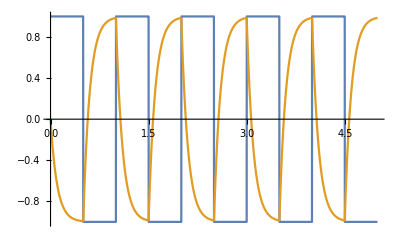

```mathematica
{RVal,CVal}={1.0,0.1};
TMax=5;
V=SquareWave
qSol=NDSolveValue[{q[t]/CVal+RVal q'[t]+V[t]==0,q[0]==0},q,{t,0, TMax}];
Plot[{V[t],qSol[t]/CVal},{t,0, TMax}]
```

TriangleWave

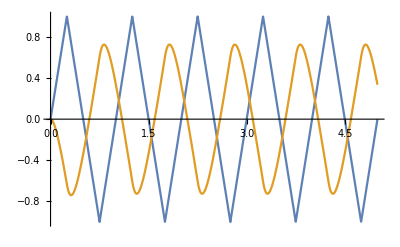

```mathematica
{RVal,CVal}={1.0,0.1};
TMax=5;
V=TriangleWave
qSol=NDSolveValue[{q[t]/CVal+RVal q'[t]+V[t]==0,q[0]==0},q,{t,0, TMax}];
Plot[{V[t],qSol[t]/CVal},{t,0, TMax}]
```

SawtoothWave

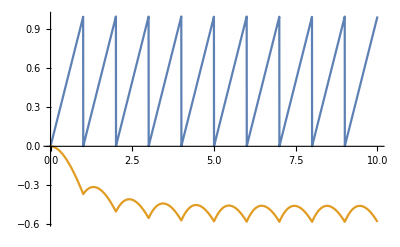

```mathematica
{RVal,CVal}={1.0,1};
TMax=10;
V=SawtoothWave
qSol=NDSolveValue[{q[t]/CVal+RVal q'[t]+V[t]==0,q[0]==0},q,{t,0, TMax}];
Plot[{V[t],qSol[t]/CVal},{t,0, TMax}]
```

Sin

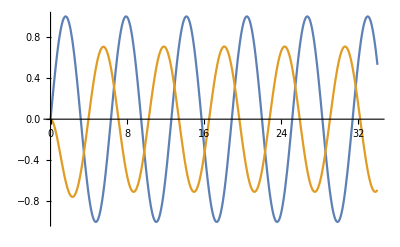

```mathematica
{RVal,CVal}={1.0,1};
TMax=34;
V=Sin
qSol=NDSolveValue[{q[t]/CVal+RVal q'[t]+V[t]==0,q[0]==0},q,{t,0, TMax}];
Plot[{V[t],qSol[t]/CVal},{t,0, TMax}]
```

```mathematica
SawtoothWave
```

SawtoothWave

```mathematica
Information[SawtoothWave]
```

## LRC Circuit

SquareWave[t]

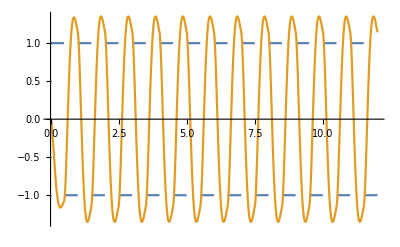

```mathematica
{RVal,CVal,LVal}={1.0,0.1,0.1};
TMax=12;
V[t_]=SquareWave[t]
qSol=NDSolveValue[{q[t]/CVal+RVal q'[t]+LVal q''[t]+V[t]==0,q'[0]==0,q[0]==0},q,{t,0, TMax}];
Plot[{V[t],qSol[t]/CVal},{t,0, TMax}]
```

```mathematica
?SquareWave
```

## References

[1]  Rössler, O. E.  1976
“An Equation for Continuous Chaos”, Physics Letters, 57A (5): 397–398.

[2]  Plazas,D. and Cardenas-Rodriques, J. S.  2019
“Chaotic Rössler System based on Circuits”, https://www.researchgate.net/publication/334634999_Linear_Analysis_of_Rossler_System_based_on_Circuits

[3]  Struthers, A. and Potter, M.  2019
“Differential Equations for Scientists and Engineers”, Springer

[4]  Zill D. G. (various editions and years) 
“A First Course in Differential equations with Modeling Applications”

[5]  Analog Devices
“Low Cost Analog Multiplier AD633”
https://www.analog.com/media/en/technical-documentation/data-sheets/ad633.pdf